## 3.029 Data-Viz Hour 04/12/2022

Scientific Data Link:

https://www.nature.com/articles/s41597-022-01215-7

## Aluminum Alloys from Patents

Three files

Readme.txt (always good to check)

property.csv

composition.csv

```mathematica
rawPropertyData=Import["/home/george/Downloads/property.csv","Data"];
rawPropertyData[[1]]
rawPropertyData=Rest[rawPropertyData];
```

{doi,name,series,caption,AA_des,YS,UTS,temper,elong,flag,flag_note}

1268 alloy compositions in our dataset

```mathematica
rawPropertyData//Dimensions
```

{1268,11}

```mathematica
TableForm[rawPropertyData[[;;10]]]
```

10.1016/j.msea.2003.10.237 | ECAE | 1000 | Room temperature tensile properties of the 1560 alloy | 1560 | 355 | 435 |  |  | TRUE | SPD: ECAE
10.1016/j.msea.2003.10.237 |  | 1000 | Room temperature tensile properties of the 1560 alloy | 1560 | 350 | 415 |  |  | TRUE | SPD: ECAE
10.1016/j.msea.2003.10.237 |  | 1000 | Room temperature tensile properties of the 1560 alloy | 1560 | 195 | 380 |  |  | TRUE | SPD: ECAE
10.1016/j.msea.2009.11.069 | Al 1100 | 1000 | Specifications of the commercial purity aluminum. | 1100 | 169.1 | 186.4 |  | 6.02 | FALSE | 
10.1007/s11661-016-3375-0 | 1.5 | 1000 | Tensile Properties of Al 1100-H18 Sheets | 1100 | 180.2 | 191.3 | H18 |  | FALSE | 
10.1007/s11661-016-3375-0 | 2 | 1000 | Tensile Properties of Al 1100-H18 Sheets | 1100 | 177.2 | 188.3 | H18 |  | FALSE | 
10.1007/s11661-016-3375-0 | 2.5 | 1000 | Tensile Properties of Al 1100-H18 Sheets | 1100 | 165.3 | 175.3 | H18 |  | FALSE | 
10.1016/j.msea.2012.12.046 | As-received | 1000 | Tensile properties of Cp Al 1050 in various swaged conditions. | 1050 | 20 | 72 |  | 120 | FALSE | 
10.1016/j.msea.2012.12.046 | ph=0.4 | 1000 | Tensile properties of Cp Al 1050 in various swaged conditions. | 1050 | 87 | 91 |  | 18 | FALSE | 
10.1016/j.msea.2012.12.046 | ph=0.8 | 1000 | Tensile properties of Cp Al 1050 in various swaged conditions. | 1050 | 111 | 112 |  | 15.1 | FALSE |

Let’s group by alloy-designation number

```mathematica
Keys[sortedByAlloyDesignation=KeySelect[KeySort[GroupBy[rawPropertyData,#[[5]]&]],IntegerQ]]
```

{1000,1050,1100,1400,1560,2009,2014,2017,2024,2050,2060,2124,2139,2195,2198,2219,2519,2524,3003,4004,4032,5052,5056,5059,5083,5086,5182,5556,5754,6005,6016,6061,6063,6082,6111,6181,6201,7005,7010,7015,7017,7020,7034,7039,7050,7055,7068,7075,7150,7175,7449,7475,8090}

```mathematica
sortedByAlloyDesignation
```

{1000,1050,1100,1400,1560,2009,2014,2017,2024,2050,2060,2124,2139,2195,2198,2219,2519,2524,3003,4004,4032,5052,5056,5059,5083,5086,5182,5556,5754,6005,6016,6061,6063,6082,6111,6181,6201,7005,7010,7015,7017,7020,7034,7039,7050,7055,7068,7075,7150,7175,7449,7475,8090}

Numeric values for Yield Stress for each alloy designation

Let’s start by plotting each of these as a single point

```mathematica
yieldStress=Select[Select[#,NumberQ]&/@sortedByAlloyDesignation[[All,All,6]],Length[#]>0&];
```

```mathematica
rotateLabel=Rotate[Column[{#,Invisible[#]}],π/4]&
```

#1
#1&

```mathematica
?Invisible
```

```mathematica
Sort[Mean/@yieldStress]
```

<|3003→226/3,5754→165/2,1050→96.8929,6181→127,6063→847/6,6016→3121/22,6111→151.27,1100→172.95,5052→183.182,5086→185,6082→193.591,5556→201,6061→220.379,5182→443/2,5083→237.522,5059→250.367,1400→757/3,2219→254.509,6005→773/3,2124→1049/4,1000→267.55,2017→269.207,1560→276,7005→290,7020→611/2,2024→305.558,2009→313.051,2524→340.992,2014→341,4032→685/2,7039→352,7017→1084/3,8090→394,2060→421,7075→421.417,7475→432.106,2198→1315/3,2050→1340/3,7050→471.717,7175→479,2195→8147/17,2139→480,7010→484,7449→2011/4,7150→6148/11,7055→9779/17,7034→1205/2|>

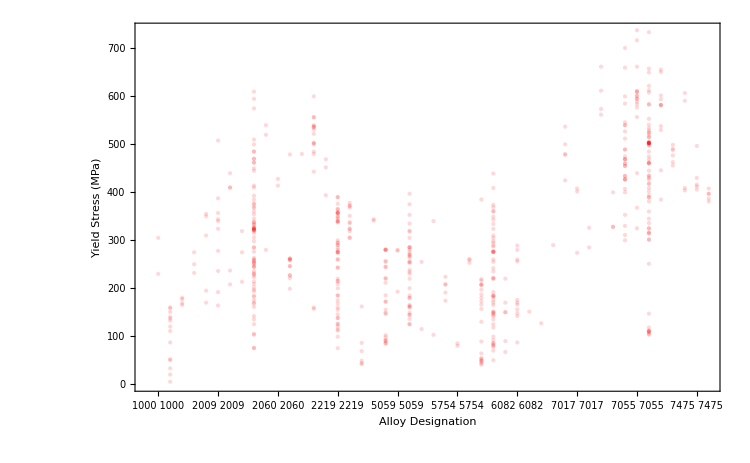

```mathematica
ListPlot[Join@@MapIndexed[Thread[{#2//First,#1}]&,yieldStress//Values],Frame->True,FrameStyle->Directive[Black,Thick],ImageSize->750,LabelStyle->Directive[12,Black],FrameLabel->{"Alloy Designation","Yield Stress (MPa)"},PlotStyle->Directive[PointSize[Large],Opacity[0.15],Red],FrameTicks->{{Automatic,None},{Thread[{Range[Length[yieldStress]],rotateLabel/@Keys[yieldStress]}],Automatic}}]
```

Let’s quickly plot the sorted means as a bar chart

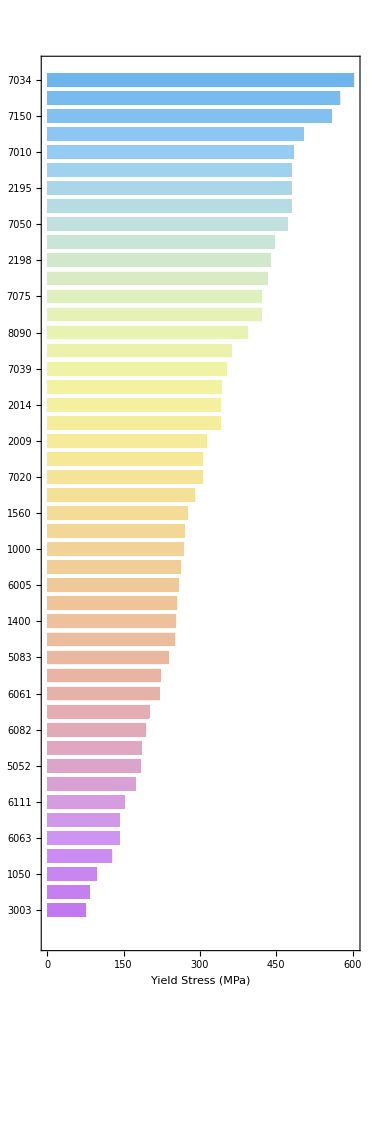

```mathematica
With[{sortedMeans=Sort[Mean/@yieldStress]},
BarChart[sortedMeans,BarOrigin->Left,ChartLabels->Keys[sortedMeans],ImageSize->375,LabelStyle->Directive[16,Black],ChartStyle->"Pastel",AspectRatio->3,Frame->True,FrameLabel->{None,"Yield Stress (MPa)"}]
]
```